1266

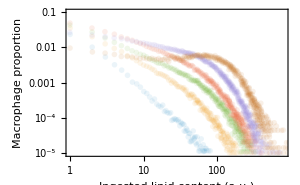

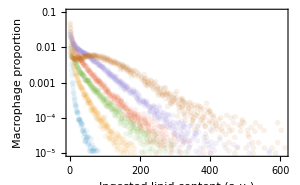

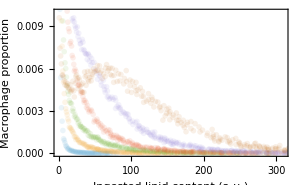

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[loglikelihood];

loglikelihood[{e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,loglikelihoodL,outcome,λ,Loutput},


rhsVecfunction[v_?VectorQ,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax] *)
x=βvec*v;
h=ListConvolve[fvec,ListConvolve[x,v,{1,-1},0],{1,-1},0];
Take[h,n]-x
];

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));


(*ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]+Last[βvec]*(1-Total[u[t]])),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,5}];
loglikelihoodL=Sum[-Log[lipiddata[[i]][[2]]*σL*Sqrt[2 Pi]]-1/(2*σL^2)*(Log[lipiddata[[i]][[2]]]-Log[Loutput[[i]]])^2,{i,2,5}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodL,Reals],loglikelihoodM+loglikelihoodL,-10^(6)]
]

(* Plot function *)

plots[{e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,modeldistributionplotloglinear,modeldistributionplotloglog},



rhsVecfunction[v_?VectorQ,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax] *)
x=βvec*v;
h=ListConvolve[fvec,ListConvolve[x,v,{1,-1},0],{1,-1},0];
Take[h,n]-x
];

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

(*ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]+Last[βvec]*(1-Total[u[t]])),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];


modeldistributionplot=ListPlot[moutput,PlotRange->{{0,300},{0,0.02}},ImageSize->300,Joined->True];
modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,50},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,50},PlotRange->{{-0.5,50},{-0.05,50}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean ingested lipid (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];


Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot]},{Show[distributionlinearplot48,modeldistributionplot],Show[distributionloglinearplot48,modeldistributionplotloglinear](*,Show[distributionloglogplot48,modeldistributionplotloglog]*)}}]
]
```

```mathematica
(* MLE: βvec = β0 *)
nstep=1;
{eval,cvval,β0val,σMval,σmval}={0.4,0.1,1/80,0.5,0.5};
NMaximize[{loglikelihood[{100*e,cv,β0,0,1,σM,σL}],0.01<e<1,0.01<cv<1,0.001<β0<0.2,0.01<σM<3,0.01<σL<1},{e,cv,β0,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,σM,σL},loglikelihood[{100*e,cv,β0,0,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.545741,0.269039,0.00720435,0.807769,0.502642},-8.08053}

Current x: {{0.539602,0.215605,0.00688551,0.805549,0.474326},-8.03004}

{-8.03004,{e→0.539602,cv→0.215605,β0→0.00688551,σM→0.805549,σL→0.474326}}

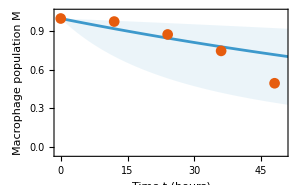
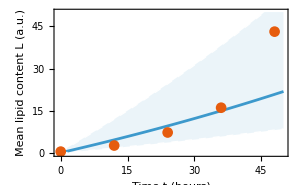
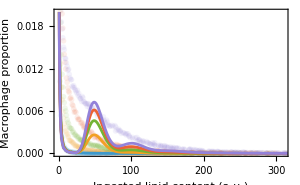
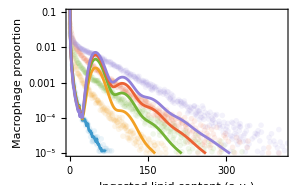
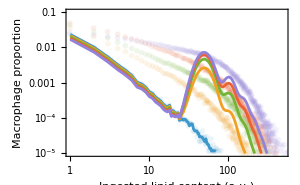
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0,0,1,σM,σL}/.{e->0.5396021317204953,cv->0.21560524940573067,β0->0.0068855090625788255,σM->0.8055491152408989,σL->0.4743257500360418}]
```

```mathematica
(* MLE: βvec = β0*Exp[β1*t] - independent of cv! *)
nstep=1;
{eval,cvval,β0val,β1val,σMval,σLval}={0.4,0.1,0.3,0.05,0.5,0.5};
NMaximize[{loglikelihood[{100*e,cvval,β0/100,β1,1,σM,σL}],0.01<e<1,0.01<β0<1,0.01<β1<1,0.01<σM<3,0.01<σL<1},{e,β0,β1,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cvval,β0,β1,σM,σL},loglikelihood[{100*e,cvval,β0/100,β1,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.327846,0.1,0.448499,0.0491485,0.645766,0.0980869},0.201121}

Current x: {{0.317921,0.1,0.476379,0.0464903,0.63075,0.0457805},1.90659}

Current x: {{0.319149,0.1,0.474773,0.0465556,0.708627,0.0448265},1.9808}

Current x: {{0.417182,0.1,0.342168,0.0509234,0.399621,0.0528726},2.97337}

Current x: {{0.493229,0.1,0.286308,0.0526943,0.299193,0.0490144},3.67132}

Current x: {{0.577166,0.1,0.241996,0.0539737,0.305522,0.0546605},4.19594}

Current x: {{0.566952,0.1,0.251236,0.0530162,0.329978,0.0537724},4.262}

{4.2622,{e→0.565549,β0→0.251765,β1→0.0530115,σM→0.330353,σL→0.0535792}}

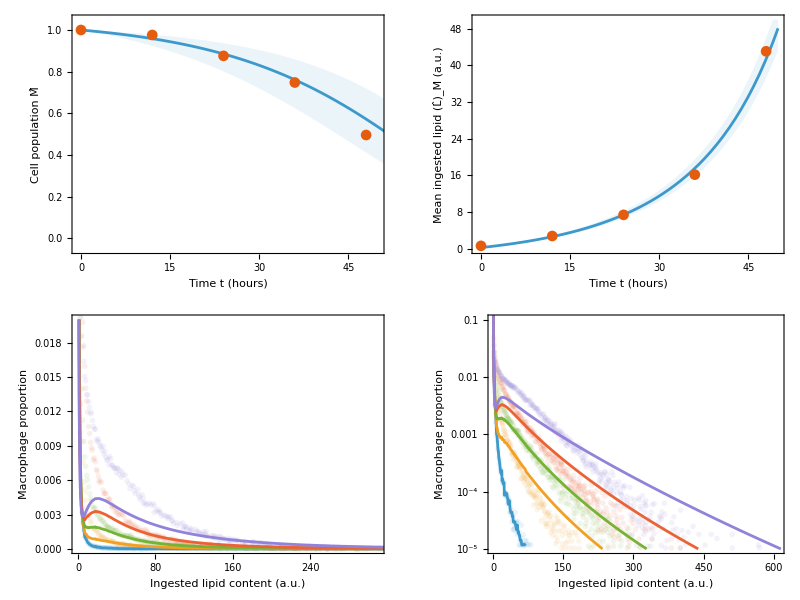

```mathematica
plots[{100*e,cv,β0/100,β1,1,σM,σL}/.{e->0.5655485335030122,cv->1,β0->0.25176537086748785,β1->0.0530114657705847,σM->0.33035288830176845,σL->0.0535792203124518}]
```

```mathematica
(* MLE: βvec = β0+β1*idx *)
nstep=1;
{eval,cvval,β0val,β1val,σMval,σLval}={0.12177390388387464,0.7655520841011598,1.5592251365614875,0.16509286494405248,1.3337895859782167,0.08935303066888678};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σL}],0.01<e<1,0.01<cv<1,0.1<β0<10,0.01<β1<1,0.01<σM<3,0.01<σL<1},{e,cv,β0,β1,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,σM,σL},loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

{-2.60916,{e→0.121774,cv→0.765552,β0→1.55923,β1→0.165093,σM→1.33379,σL→0.0536307}}

```mathematica
nstep=1;
{eval,cvval,β0val,β1val,σMval,σLval}={0.12177390388387464,0.7655520841011598,1.5592251365614875,0.16509286494405248,1.3337895859782167,0.05363073479409445};
FindMaximum[{loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σL}],0.01<e<1,0.01<cv<1,0.01<β0<10,0.1<β1<1000,0.01<σM<3,0.01<σL<1},{{e,eval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σL,σLval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,cv,β0,β1,1,σM,σL},loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.121774,0.765552,1.55923,0.165093,1,1.33379,0.0536307},-2.60916}

Current x: {{0.121774,0.765552,1.55923,0.165093,1,1.33379,0.0536307},-2.60912}

Current x: {{0.121774,0.765552,1.55923,0.165093,1,1.33379,0.0536307},-2.60912}

Current x: {{0.121774,0.765552,1.55923,0.165093,1,1.33379,0.0536307},-2.60912}

«1 more identical outputs»

$Aborted

-2.60916

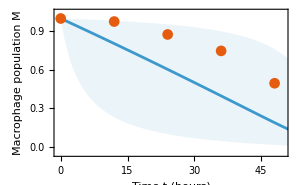
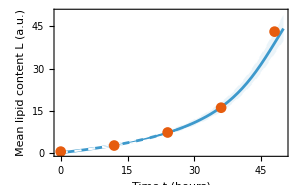
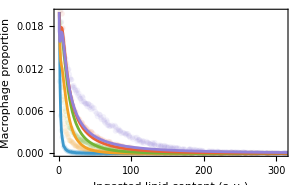
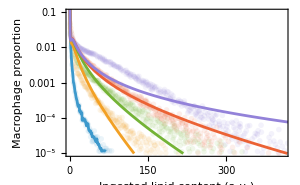
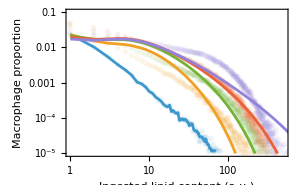
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σL}/.{e->0.12177390388387464,cv->0.7655520841011598,β0->1.5592251365614875,β1->0.16509286494405248,σM->1.3337895859782167,σL->0.05363073479409445}]
plots[{100*e,cv,β0/100,β1/100,1,σM,σL}/.{e->0.12177390388387464,cv->0.7655520841011598,β0->1.5592251365614875,β1->0.16509286494405248,σM->1.3337895859782167,σL->0.05363073479409445}]
```

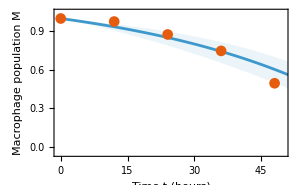
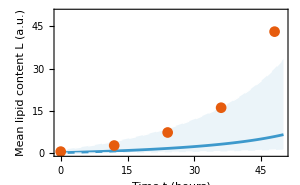
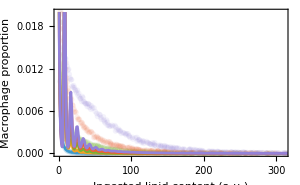
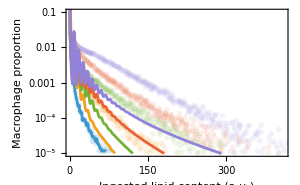
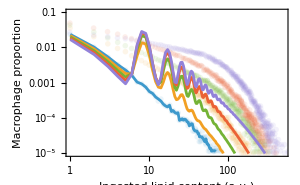
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,β1/100,1,σM,σL}/.{e->0.1,cv->0.1,β0->0.4,β1->0.3,σM->0.2181099221481927,σL->0.824743741769985}]
```

```mathematica
(* MLE: βvec = β1/(1+(β1-β0)/β0*Exp[-t/q] - independent of cv! tends to β1->infinity case *)
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.74270049747501,0.1,0.09155846845171661,0.9964731101780913,5.334136205905133,0.4778165611630636,0.22784210170928543};
NMaximize[{loglikelihood[{100*e,cvval,β0/100,β1/100,q,σM,σL}],0.01<e<1,0.01<β0<1,0.1<β1<100,0.01<q<100,0.01<σM<3,0.01<σL<1},{e,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cvval,β0,β1,q,σM,σL},loglikelihood[{100*e,cvval,β0/100,β1/100,q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

```mathematica
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.5682828494527594,0.1,0.25,100,18,0.14130225018159157,0.25834215832022706};
FindMaximum[{loglikelihood[{100*e,cvval,β0/100,β1,q,σM,σm}],0.1<e<1,0.01<β0<1,0.1<β1<1000,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,cvval,β0,β1,q,σM,σm},loglikelihood[{100*e,cvval,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.568283,0.1,0.25,100.,18.,0.141302,0.5},-7.00617}

Current x: {{0.563525,0.1,0.243316,100.,17.9923,0.178272,0.419792},-3.4706}

Current x: {{0.558502,0.1,0.24177,100.,17.9875,0.193359,0.216945},-0.374696}

Current x: {{0.558811,0.1,0.240786,100.,17.9875,0.202733,0.114507},1.99303}

Current x: {{0.562964,0.1,0.239443,100.,17.9977,0.206272,0.0627762},3.02985}

Current x: {{0.563411,0.1,0.258335,188.142,19.2003,0.269783,0.044958},3.82099}

Current x: {{0.565464,0.1,0.253056,687.979,18.9371,0.307923,0.050572},4.22252}

Current x: {{0.564418,0.1,0.25249,504.472,18.8804,0.328663,0.0537855},4.2616}

Current x: {{0.564226,0.1,0.252445,500.487,18.8737,0.332921,0.0543855},4.26076}

Current x: {{0.565523,0.1,0.251774,500.85,18.8635,0.330418,0.05359},4.26204}

Current x: {{0.565513,0.1,0.251782,512.803,18.8637,0.330428,0.0536044},4.26204}

Current x: {{0.565549,0.1,0.251763,524.681,18.8635,0.330355,0.0535827},4.26205}

$Aborted

```mathematica
(* MLE: βvec = β0+(β1-β0)*(1-Exp[-idx/q] *)
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.14790624221009246,0.14249866574071965,1.1513887463275798,0.6732543174865205,3.283709978027588,1.4806159488920347,0.024993724556705354};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}],0.01<e<1,0.01<cv<1,0.01<β0<10,0.01<β1<10,0.01<q<10,0.01<σM<3,0.01<σL<1},{e,cv,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,qval,σMval,σLval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,q,σM,σL},loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.147906,0.142499,1.15139,0.673254,3.28371,1.48062,0.0249937},1.45276}

Current x: {{0.144584,0.1434,1.18488,0.679152,3.31647,1.48939,0.023946},1.57297}

Current x: {{0.13043,0.154477,1.35507,0.71393,3.53287,1.54036,0.0187111},2.08217}

Current x: {{0.114025,0.183342,1.60795,0.769147,3.9199,1.62243,0.0158697},2.35993}

Current x: {{0.111413,0.189481,1.65359,0.781509,3.99726,1.63817,0.0156897},2.37462}

{2.37502,{e→0.111118,cv→0.190346,β0→1.65939,β1→0.782817,q→4.00745,σM→1.64019,σL→0.0156587}}

```mathematica
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.14906006481771836,0.14064294335889022,1.1446842162255093,0.6705798585107974,3.2836555982955673,1.4805733124385647,0.02434018045772451};
FindMaximum[{loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}],0.01<e<1,0.01<cv<1,0.01<β0<10,0.01<β1<10,0.01<q<10,0.01<σM<3,0.01<σL<1},{{e,eval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σL,σLval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,cv,β0,β1,q,σM,σL},loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.14906,0.140643,1.14468,0.67058,3.28366,1.48057,0.0243402},1.41419}

Current x: {{0.148863,0.140671,1.14484,0.6707,3.28364,1.48057,0.0246624},1.43136}

Current x: {{0.148743,0.140695,1.14542,0.671139,3.2836,1.48058,0.025016},1.43188}

Current x: {{0.148485,0.141241,1.14699,0.671985,3.28354,1.48058,0.0251222},1.43707}

Current x: {{0.148424,0.141302,1.1475,0.672075,3.28352,1.48059,0.0251271},1.43877}

Current x: {{0.148034,0.142077,1.14979,0.673497,3.28358,1.4806,0.0250384},1.44697}

Current x: {{0.147988,0.142201,1.15043,0.673337,3.2836,1.48061,0.025023},1.44937}

Current x: {{0.147969,0.142246,1.15068,0.673296,3.28362,1.48061,0.0250165},1.45026}

Current x: {{0.147906,0.142499,1.15139,0.673254,3.28371,1.48062,0.0249937},1.45276}

$Aborted